```mathematica
(*Exercício 1.1*)
sundaram[n_] :=
Module[{L = Range[n],i=1,j},
While[2 i (i+1)<= n,
If[L[[i]] != "REMOVIDO",
Do[L[[j]]="REMOVIDO", {j,3i+1,n,2i+1}]];
i = i+1
];
Table[If[x!= "REMOVIDO", 2x+1, Nothing], {x,L}]]
sundaram/@Range[7]//Column
sundaram[20]
Prime[Range[13]]
```

{3}
{3,5}
{3,5,7}
{3,5,7}
{3,5,7,11}
{3,5,7,11,13}
{3,5,7,11,13}

{3,5,7,11,13,17,19,23,29,31,37,41}

{2,3,5,7,11,13,17,19,23,29,31,37,41}

```mathematica
(*sundaram[n] retorna os primos ímpares até 2n+1, inclusive.*)
```

```mathematica
(*Exercício 1.2*)
sundquot[n_] := Length[sundaram[n]] Log[n] / n
(*sabemos que length[sundaram[n]] = pi(2n+1) - 1. ora,
(pi(2n+1) - 1)/(n/logn)=(pi(2n+1))/((2n+1) log(2n+1))(2n+1)/n (log(2n+1))/(log(2n))(log(2n))/(log(n))(pi(2n+1)-1)/(pi(2n+1)).
o primeiro termo vai para 1 pelo teorema dos números primos.
o segundo termo vai para 2.
o numerador terceiro termo é log(2n+1)-log(2n)+log(2n) = log(2n) + 1/(algo entre 2n e 2n+1) por lagrange. dividindo por log(2n), obtemos 1+(coisa que tende para zero).
o quarto é (log(n) + log(2))/(log(n))->1
o quinto é 1 porque pi(n) -> ∞.
logo o limite desejado é o produto destes todos, que é 2.*)
sundquot/@(10^Range[7])//N
```

{1.61181,2.07233,2.08614,2.08246,2.07037,2.05757,2.04797}

```mathematica
(*os testes computacionais confirmam que sundquot há-de tender para 2.*)
```

```mathematica
(*Exercício 1.3*)
redundancia[n_] :=
Module[{L = Range[n],i=1,j, count=0},
While[2 i (i+1)<= n,
If[L[[i]] != "REMOVIDO",
Do[If[L[[j]]=="REMOVIDO", count++,L[[j]]="REMOVIDO"], {j,3i+1,n,2i+1}]];
i = i+1
];
count]
redundancia/@Range[10,50,10]
```

{0,1,4,6,6}

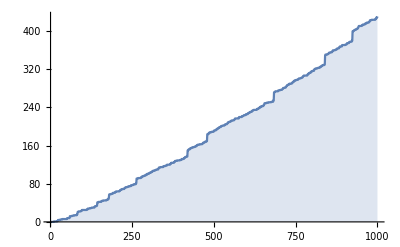

```mathematica
(*Fazer o gráfico de redundancia[n]*)
DiscretePlot[redundancia[n], {n,1,1000}]
```

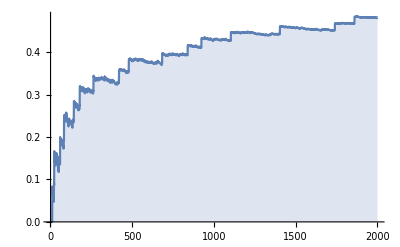

```mathematica
(*Parece mais ou menos linear*)
DiscretePlot[redundancia[n]/n, {n,1,2000}]
```

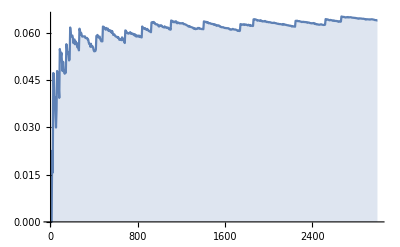

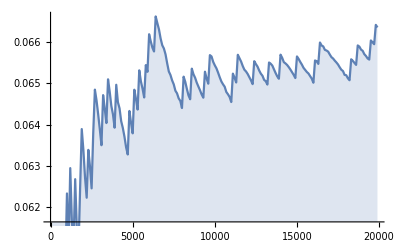

```mathematica
(*Crescimento logaritmico?*)
DiscretePlot[redundancia[n]/(n Log[n]), {n,1,3000,5}]
DiscretePlot[redundancia[n]/(n Log[n]), {n,1,20000,100}]
```

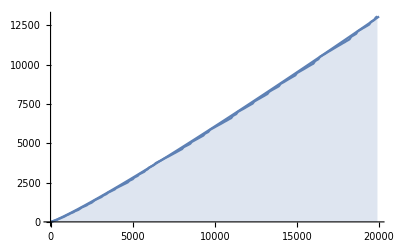

```mathematica
(*Parece estabilizar mais ou menos em aproximadamente 0.066*)
Show[DiscretePlot[redundancia[n], {n,1,20000,100}],Plot[0.066 x Log[x], {x, 1,20000}]]
```

```mathematica
(*Exercício 1.4*)
(*O crivo de Sundaram funciona de forma semelhante ao de Eratóstenes, iterando sobre os números ainda não removidos, e removendo todos os seus múltiplos. No entanto, isto é ligeiramente ofuscado por estes estarem representados por números que não o próprio.
Para explicar melhor o funcionamento, comecemos com o crivo de Eratóstenes e modifiquemo-lo para obter o de Sundaram.
Primeiro que tudo: eliminamos imediatamente os números pares, começando apenas com 3,5,7,...
Consequentemente, quando o algoritmo chega a um número, digamos 5, basta remover os seus múltiplos ímpares, 5, 15, 25,...
A última modificação é a seguinte: o número ímpar 2k+1 é representado por k. Ou seja, começando com a lista 1,2,3,...,n esta representa realmente a lista 3,5,7,...,2n+1
O funcionamento do algoritmo fica agora evidente, com base no de Eratóstenes. Estamos a iterar sobre os elementos da lista, apenas enquanto o quadrado dos elementos for inferior ou igual a 2n+1 (porque um número que não seja primo tem pelo menos um divisor menor ou igual que a sua raíz). Ora, i representa um número cujo quadrado é <= 2n+1 sse (2i+1)^2 <= 2n+1 sse 4i^2 + 4i <= 2n, sse 2 i (i+1) <= n, que é precisamente a condição do While.
Agora, chegado ao i-ésimo elemento da lista, se este não tiver sido removido, removemos os múltiplos ímpares correspondentes. O índice i representa o número 2i+1, que quando multiplicado por (2k+1) dá (2k+1)(2i+1) = 4ki + 2(k+i) + 1 = 2 (2ki + k + i) + 1. Logo, o primeiro múltiplo ímpar que não o próprio tem índice j = 2i+1+i=3i+1 (que é o valor inicial de j), e aumentar o múltiplo (incrementar o k) corresponde a somar 2i+1 a j, o que se verifica no crivo.

Isto termina a verificação de que o crivo de Sundaram corresponde ao crivo de Eratóstenes com os pares removidos e os ímpares 2i+1 substituídos pelo seu "índice" i. Isto justifica que o crivo retorna os primos, e como os pares foram removido, precisamente os primos ímpares.*)
```

```mathematica
(*Exercício 2*)
(*Exercício 2.1*)
rShuffle[deck_]:= Riffle[deck[[;;Ceiling[Length[deck]/2]]], deck[[Ceiling[Length[deck]/2]+1;;]]]
(*Exercício 2.2*)
Nest[rShuffle,Range[8],3]
Nest[rShuffle,Range[52],8]
```

{1,2,3,4,5,6,7,8}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

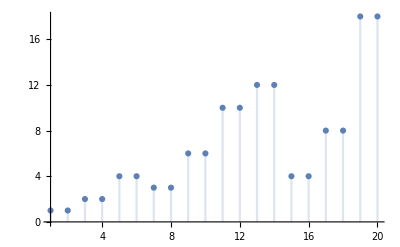

```mathematica
(*Exercício 2.3*)
ord[n_] := Module[{shuffled = rShuffle[Range[n]], shuffles = 1},
While[shuffled != Range[n],shuffles++; shuffled=rShuffle[shuffled]];
shuffles]
DiscretePlot[ord[i],{i,1,20}]
(*Conjetura: ord(i) = ord(i+1) para i ímpar*)
```

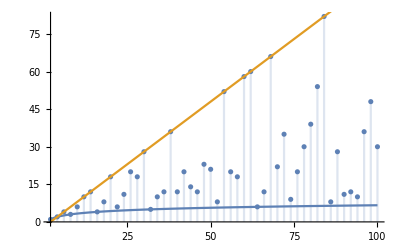

```mathematica
(*Exercício 2.4*)
(*Conjetura: para i par, i>2, log(i)/log(2) ≤ ord(i) ≤ i-2*)
Show[DiscretePlot[ord[i],{i,2,100,2}],Plot[{Log[x]/Log[2],x-2},{x,2,100}]]
```

```mathematica
(*Exercício 2.5*)
Table[If[ord[i] == Log[i]/Log[2], i,Nothing],{i,2,400,2}]
(*Claramente as potências de 2*)
```

{2,4,8,16,32,64,128,256}

```mathematica
(*Exercício 3*)
genContinuedFraction[a_, b_] := Module[{acc = Last[b]},
Do[acc = b[[i]] + a[[i]]/acc,{i,Length[a],1,-1}];
acc]
(*Testar o código*)
genContinuedFraction[{a1,a2,a3,a4},{b0,b1,b2,b3,b4}]
```

b0+a1/(b1+a2/(b2+a3/(b3+a4/b4)))

```mathematica
(*Exercício 3.1*)
Log[2]//N
Table[Sum[(-1.)^(k-1)/k,{k,1,10^i}] ,{i,5}]
Table[
genContinuedFraction[ (* 0, 1, 1, 1, ... *)
Prepend[ Range[i-1]^2,1],
Prepend[ConstantArray[1.,i],0.] (* 1, 1^2, 2^2, 3^2, ...*)
], {i, {10,100,1000,10000,100000}}]
(*verificamos que o somatório com k=1 até N parece ser idêntico ao N-ésimo convergente da fração contínua generalizada, e que ambos convergem (algo lentamente) para log(2).*)
```

0.693147

{0.645635,0.688172,0.692647,0.693097,0.693142}

{0.645635,0.688172,0.692647,0.693097,0.693142}

```mathematica
(*Exercício 3.2*)
genContinuedFraction[{2,3,4,5},{2,2,3,4,5}] // N
(*parece ser e*)
```

2.71698

```mathematica
next = genContinuedFraction[{2,1,1,1},{1,3,12,20,28}] // N
2 next
Sqrt[next]
Tan[next]
ArcTan[next]
next^2
(*parece ser √e*)
```

1.64872

3.29744

1.28403

-12.8069

1.02559

2.71828

```mathematica
next = genContinuedFraction[{1,1,2^2,3^2,4^2,5^2},{0,2,6,10,14,18}] // N
Pi/next
E/next
Sqrt[next]
Tan[next]
ArcTan[next]
next^2
(*arctg(1/2)*)
```

0.463648

6.77582

5.86282

0.680917

0.5

0.434145

0.214969

```mathematica
(*Exercício 3.3*)
aprox1[n_] := genContinuedFraction[
Prepend[(2 Range[n]-1)^2,4],
Join[{0,1},ConstantArray[2.,n-1]]
]
aprox2[n_] := genContinuedFraction[
(2Range[n]-1)^2, Prepend[ConstantArray[6.,n],3]
]
aprox3[n_] := genContinuedFraction[
Prepend[Range[n]^2,4], Prepend[2Range[n]-1,0.]
]
```

1 | 2 | 3.16667 | 2.
2 | 3.46667 | 3.13333 | 3.25
3 | 2.89524 | 3.14524 | 3.12821
4 | 3.33968 | 3.13968 | 3.14349
5 | 2.97605 | 3.14271 | 3.14131
6 | 3.28374 | 3.14088 | 3.14164
7 | 3.01707 | 3.14207 | 3.14159
8 | 3.25237 | 3.14125 | 3.14159
9 | 3.04184 | 3.14184 | 3.14159
10 | 3.23232 | 3.14141 | 3.14159

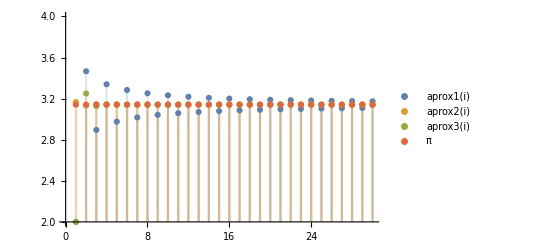

```mathematica
TableForm[
Table[{i,aprox1[i],aprox2[i],aprox3[i]},{i,1,10}]
]
DiscretePlot[{aprox1[i],aprox2[i],aprox3[i],π},{i,1,30}, PlotLegends->"Expressions",PlotRange->{2,4}]
(*Tanto pela tabela como pela imagem, é claro que aprox1 converge bastante lentamente, aprox3 converge muito rapidamente (tendo 5 casas decimais, mais a das unidades, corretas após apenas 7 iteradas), e aprox2 está algures no meio.*)
```

```mathematica
(*Exercício 3.4*)
(*
a) Consideramos a fração contínua generalizada -b + -c/(-b+-c/(-b+...))
Os seus convergentes (talvez) aproximam soluções de x^2 + b x + c = 0.
*)
solvequad[b_, c_, n_] := genContinuedFraction[
ConstantArray[-c,n], ConstantArray[-b,n+1]
]
solvequad[b,c,3]
```

-b-c/(-b-c/(-b+c/b))

```mathematica
(*b) *)
TableForm[
Table[{solvequad[-4,4,n],solvequad[-4,2,n],solvequad[-4,6,n]}//N,{n,1,20}]
]
```

3. | 3.5 | 2.5
2.66667 | 3.42857 | 1.6
2.5 | 3.41667 | 0.25
2.4 | 3.41463 | -20.
2.33333 | 3.41429 | 4.3
2.28571 | 3.41423 | 2.60465
2.25 | 3.41422 | 1.69643
2.22222 | 3.41421 | 0.463158
2.2 | 3.41421 | -8.95455
2.18182 | 3.41421 | 4.67005
2.16667 | 3.41421 | 2.71522
2.15385 | 3.41421 | 1.79023
2.14286 | 3.41421 | 0.648479
2.13333 | 3.41421 | -5.25241
2.125 | 3.41421 | 5.14233
2.11765 | 3.41421 | 2.83321
2.11111 | 3.41421 | 1.88226
2.10526 | 3.41421 | 0.812349
2.1 | 3.41421 | -3.38599
2.09524 | 3.41421 | 5.77201

```mathematica
Solve[x^2 - 4x +4 == 0]
Solve[x^2 - 4x + 2 == 0]//N
Solve[x^2 - 4x + 8 == 0]
(*Concluímos que em pelo menos alguns casos (o segundo) a nossa fração contínua generalizada converge (rapidamente, até) para uma solução da equação. No primeiro caso a fração contínua parece também convergir, mas muito lentamente, para a única solução. Finalmente, no terceiro caso não parece haver convergência: a fração oscila radicalmente. Isto faz algum sentido, visto que os convergentes são sempre reais mas a solução tem soluções complexas (não reais).*)
```

{{x→2},{x→2}}

{{x→0.585786},{x→3.41421}}

{{x→2-2 ⅈ},{x→2+2 ⅈ}}

```mathematica
(*c) *)
(*i) não temos convergência, ou sequer todos os convergentes: o primeiro convergente é logo
-b + -c/-b = 0 + -c/0, que não está bem-definido por ter divisão por zero. *)
Table[solvequad[0,c,i],{i,1,4}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{ComplexInfinity,0,ComplexInfinity,0}

```mathematica
(*ii) *)
(*simplificando o lado esquerdo, para x = √(-c),
2p + (-c-p^2)/(x + p) = 2p + (x-p)(-c-p^2)/(x^2 - p^2) = 2p + (x-p)(-c-p^2)/(-c-p^2) = x + p,
como desejado.*)
aproxsqrt[c_,p_,n_] := (*usa o método para aproximar √(-c)*)
(*sendo y = x+p, queremos os convergentes da equação dada por
y = 2p + (-c-p^2)/y, que já está implementado na função solvequad:*)
solvequad[-2p,c+p^2,n]-p

TableForm[
Table[aproxsqrt[c,p,20]//N,{c,{-3,-4,-5}},{p,1,5}]
]
{Sqrt[3],Sqrt[4],Sqrt[5]}//N
(*Este método parece funcionar, convergindo rapidamente para qualquer p positivo testado (entre 1 e 5).2*)
```

1.73205 | 1.73205 | 1.73205 | 1.73205 | 1.73205
2. | 2. | 2. | 2. | 2.
2.23607 | 2.23607 | 2.23607 | 2.23607 | 2.23607

{1.73205,2.,2.23607}

```mathematica
(*iii) *)
(*
aplicamos a alínea anterior para c = -r^2 - 1, p = r. neste caso, a fração contínua de √(-c) = √(r^2 - 1) é dada por
x = p + (-c-p^2)/(2p+(-c-p^2)/(2p+...)) = r + 1/(2r+1/(2r+...)).
logo, se n = r^2 + 1, a sua raíz quadrada tem fração contínua [r,2r,2r,2r,...]. pelo outro lado, se √n tem esta fração contínua, então √n = √(r^2-1), e tomando o quadrado dos dois lados obtemos n = r^2 - 1, como desejado.
*)
```

```mathematica
(*d) *)
(* i) *)
testSolution[b_, c_] := (*Testa o método para dados b e c. Tenta detetar convergência para uma solução, retornando verde ou vermelho consoante está próximo de uma solução ou não*)
If[b==0, Yellow,
Module[{c100 = solvequad[b,c,100]},
If[Abs[c100^2 + b c100 +c ]< .01, Green,Red]
]
]
testSolution[-4,2]
testSolution[-4,4]
testSolution[-4,6]
```

RGBColor[0, 1, 0]

RGBColor[0, 1, 0]

RGBColor[1, 0, 0]

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

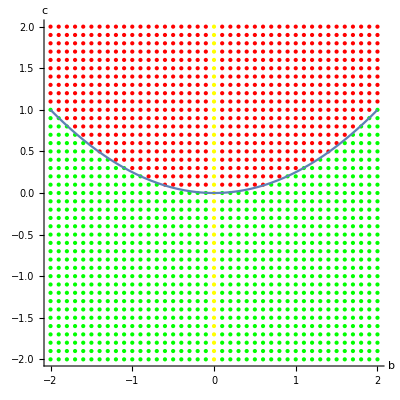

```mathematica
(*ii) e iii)*)
Show[
Graphics[
Table[{testSolution[b,c], Point[{b,c}]},{b,-2,2,.1},{c,-2,2,.1}], Axes-> True, AxesLabel-> {"b", "c"}
],
Plot[x^2/4,{x,-2,2}]]
(*Os convergentes parecem converger para uma solução sempre que b^2 > 4 c mas não b^2 < 4 c. isto faz sentido, porque as soluções são reais precisamente quando b^2 - 4 c > 0*)
```

```mathematica
Table[testSolution[b,b^2 / 4], {b,-2,2,.1}]
(*no caso b^2 = 4 c, exceto quando b= 0, temos convergência para solução. em conclusão, o método funciona sse b^2 - 4c >= 0, o que faz sentido porque isto é precisamente quando existe solução real.*)
```

{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}

```mathematica
(*Exercício 4*)
(*Exercício 4.1*)
(*Se mdc(a,b) != 1, mostramos que existem inteiros arbitrariamente grandes n tais que ax+by = n não tem soluções inteiras positivas. de facto, basta considerar n(k) = k mdc(a,b) + 1, para k inteiro. obviamente n(k)->∞, e os n(k) não são múltiplos de mdc(a,b). ora, como ax + by é sempre múltiplo de mdc(a,b) para x e y inteiro, temos que não há soluções inteiras para ax+by=n(k),e portanto não há soluções inteiras positivas.*)

(*Exercício 4.2*)
(*primeiro que tudo, mostramos que g(a,b) < ∞, para a e b coprimos positivos. pelo teorema de bezout, sabemos que ax+by = n tem sempre solução inteira, pelo que basta garantir a existência de soluções não-negativas para n grande.
note-se que dada uma solução (x,y), (x+kb,y-ka) também é solução para qualquer k inteiro. escolhendo k apropriado, podemos garantir que 0 <= x+kb < b, ou seja, existe sempre uma solução com 0 <= x < b. para esta solução, como y = (n-ax)/b e os números a e b são positivos, temos
y = (n-ax)/b >= (n-ab)/b = n/b-a.
logo, se garantirmos que n/b-a>=0, ou seja, n >= ab, existe definitivamente solução não-negativa, e portanto g(a,b) < ab.
isto é-nos útil porque garante que basta testar n até ab.
mais uma coisa: para determinar se ax+by=n tem solução não-negativa, basta verificar a solução descrita em que 0<=x<b. de facto, se houver uma outra solução não-negativa, podemos subtrair multiplos de b a x e somar multiplos de a a y de modo a obter uma solução destas.*)
solveaxby[a_,b_,n_]:= (*finds solution to ax+by=n with 0<=x<b*)
Module[{y},
Do[y =(n-a x)/b; If[IntegerQ[y],Return[{x,y}]],{x,0,b-1}]]
g[a_,b_] := If[CoprimeQ[a,b],
Do[If[solveaxby[a,b,n][[2]]< 0,Return[n]],{n,a b, 1, -1}]
,∞]
```

```mathematica
TableForm[
Table[g[a,b],{a,2,20},{b,2,20}]
]
```

∞ | 1 | ∞ | 3 | ∞ | 5 | ∞ | 7 | ∞ | 9 | ∞ | 11 | ∞ | 13 | ∞ | 15 | ∞ | 17 | ∞
1 | ∞ | 5 | 7 | ∞ | 11 | 13 | ∞ | 17 | 19 | ∞ | 23 | 25 | ∞ | 29 | 31 | ∞ | 35 | 37
∞ | 5 | ∞ | 11 | ∞ | 17 | ∞ | 23 | ∞ | 29 | ∞ | 35 | ∞ | 41 | ∞ | 47 | ∞ | 53 | ∞
3 | 7 | 11 | ∞ | 19 | 23 | 27 | 31 | ∞ | 39 | 43 | 47 | 51 | ∞ | 59 | 63 | 67 | 71 | ∞
∞ | ∞ | ∞ | 19 | ∞ | 29 | ∞ | ∞ | ∞ | 49 | ∞ | 59 | ∞ | ∞ | ∞ | 79 | ∞ | 89 | ∞
5 | 11 | 17 | 23 | 29 | ∞ | 41 | 47 | 53 | 59 | 65 | 71 | ∞ | 83 | 89 | 95 | 101 | 107 | 113
∞ | 13 | ∞ | 27 | ∞ | 41 | ∞ | 55 | ∞ | 69 | ∞ | 83 | ∞ | 97 | ∞ | 111 | ∞ | 125 | ∞
7 | ∞ | 23 | 31 | ∞ | 47 | 55 | ∞ | 71 | 79 | ∞ | 95 | 103 | ∞ | 119 | 127 | ∞ | 143 | 151
∞ | 17 | ∞ | ∞ | ∞ | 53 | ∞ | 71 | ∞ | 89 | ∞ | 107 | ∞ | ∞ | ∞ | 143 | ∞ | 161 | ∞
9 | 19 | 29 | 39 | 49 | 59 | 69 | 79 | 89 | ∞ | 109 | 119 | 129 | 139 | 149 | 159 | 169 | 179 | 189
∞ | ∞ | ∞ | 43 | ∞ | 65 | ∞ | ∞ | ∞ | 109 | ∞ | 131 | ∞ | ∞ | ∞ | 175 | ∞ | 197 | ∞
11 | 23 | 35 | 47 | 59 | 71 | 83 | 95 | 107 | 119 | 131 | ∞ | 155 | 167 | 179 | 191 | 203 | 215 | 227
∞ | 25 | ∞ | 51 | ∞ | ∞ | ∞ | 103 | ∞ | 129 | ∞ | 155 | ∞ | 181 | ∞ | 207 | ∞ | 233 | ∞
13 | ∞ | 41 | ∞ | ∞ | 83 | 97 | ∞ | ∞ | 139 | ∞ | 167 | 181 | ∞ | 209 | 223 | ∞ | 251 | ∞
∞ | 29 | ∞ | 59 | ∞ | 89 | ∞ | 119 | ∞ | 149 | ∞ | 179 | ∞ | 209 | ∞ | 239 | ∞ | 269 | ∞
15 | 31 | 47 | 63 | 79 | 95 | 111 | 127 | 143 | 159 | 175 | 191 | 207 | 223 | 239 | ∞ | 271 | 287 | 303
∞ | ∞ | ∞ | 67 | ∞ | 101 | ∞ | ∞ | ∞ | 169 | ∞ | 203 | ∞ | ∞ | ∞ | 271 | ∞ | 305 | ∞
17 | 35 | 53 | 71 | 89 | 107 | 125 | 143 | 161 | 179 | 197 | 215 | 233 | 251 | 269 | 287 | 305 | ∞ | 341
∞ | 37 | ∞ | ∞ | ∞ | 113 | ∞ | 151 | ∞ | 189 | ∞ | 227 | ∞ | ∞ | ∞ | 303 | ∞ | 341 | ∞

```mathematica
(*Na fila a=2, b ímpar, temos o padrão g(a,b) = b-2. no caso a ímpar, b=2, temos g(a,b) = a-2.
no caso a=11, b não múltiplo de 11, temos g(a,b) = 10b - 11. isto parece sugerir algo tipo (a-1)b - a = ab - a - b. logo, verificamos esta conjetura:*)
```

```mathematica
TableForm[
Table[g[a,b]-(a b - a - b),{a,2,20},{b,2,20}]
]
(*A conjetura verifica-se.*)
```

∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0
∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | ∞
∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0
∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0
∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0 | 0
∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | ∞ | 0 | ∞ | ∞ | 0 | 0 | ∞ | ∞ | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | ∞
∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0
∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0
∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞

```mathematica
(*Exercício 4.3*)
(*Raciocínio semelhante ao usado para definir o g*)
h[a_,b_] := If[CoprimeQ[a,b],
Sum[If[solveaxby[a,b,n][[2]]< 0,1,0],{n,a b, 1, -1}]
,∞]
TableForm[
Table[h[a,b],{a,2,20},{b,2,20}]
]
```

∞ | 1 | ∞ | 2 | ∞ | 3 | ∞ | 4 | ∞ | 5 | ∞ | 6 | ∞ | 7 | ∞ | 8 | ∞ | 9 | ∞
1 | ∞ | 3 | 4 | ∞ | 6 | 7 | ∞ | 9 | 10 | ∞ | 12 | 13 | ∞ | 15 | 16 | ∞ | 18 | 19
∞ | 3 | ∞ | 6 | ∞ | 9 | ∞ | 12 | ∞ | 15 | ∞ | 18 | ∞ | 21 | ∞ | 24 | ∞ | 27 | ∞
2 | 4 | 6 | ∞ | 10 | 12 | 14 | 16 | ∞ | 20 | 22 | 24 | 26 | ∞ | 30 | 32 | 34 | 36 | ∞
∞ | ∞ | ∞ | 10 | ∞ | 15 | ∞ | ∞ | ∞ | 25 | ∞ | 30 | ∞ | ∞ | ∞ | 40 | ∞ | 45 | ∞
3 | 6 | 9 | 12 | 15 | ∞ | 21 | 24 | 27 | 30 | 33 | 36 | ∞ | 42 | 45 | 48 | 51 | 54 | 57
∞ | 7 | ∞ | 14 | ∞ | 21 | ∞ | 28 | ∞ | 35 | ∞ | 42 | ∞ | 49 | ∞ | 56 | ∞ | 63 | ∞
4 | ∞ | 12 | 16 | ∞ | 24 | 28 | ∞ | 36 | 40 | ∞ | 48 | 52 | ∞ | 60 | 64 | ∞ | 72 | 76
∞ | 9 | ∞ | ∞ | ∞ | 27 | ∞ | 36 | ∞ | 45 | ∞ | 54 | ∞ | ∞ | ∞ | 72 | ∞ | 81 | ∞
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | ∞ | 55 | 60 | 65 | 70 | 75 | 80 | 85 | 90 | 95
∞ | ∞ | ∞ | 22 | ∞ | 33 | ∞ | ∞ | ∞ | 55 | ∞ | 66 | ∞ | ∞ | ∞ | 88 | ∞ | 99 | ∞
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | ∞ | 78 | 84 | 90 | 96 | 102 | 108 | 114
∞ | 13 | ∞ | 26 | ∞ | ∞ | ∞ | 52 | ∞ | 65 | ∞ | 78 | ∞ | 91 | ∞ | 104 | ∞ | 117 | ∞
7 | ∞ | 21 | ∞ | ∞ | 42 | 49 | ∞ | ∞ | 70 | ∞ | 84 | 91 | ∞ | 105 | 112 | ∞ | 126 | ∞
∞ | 15 | ∞ | 30 | ∞ | 45 | ∞ | 60 | ∞ | 75 | ∞ | 90 | ∞ | 105 | ∞ | 120 | ∞ | 135 | ∞
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96 | 104 | 112 | 120 | ∞ | 136 | 144 | 152
∞ | ∞ | ∞ | 34 | ∞ | 51 | ∞ | ∞ | ∞ | 85 | ∞ | 102 | ∞ | ∞ | ∞ | 136 | ∞ | 153 | ∞
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108 | 117 | 126 | 135 | 144 | 153 | ∞ | 171
∞ | 19 | ∞ | ∞ | ∞ | 57 | ∞ | 76 | ∞ | 95 | ∞ | 114 | ∞ | ∞ | ∞ | 152 | ∞ | 171 | ∞

```mathematica
(*Observando os casos a=11 e b não múltiplo de 11, temos
h(a,b) = 5b - 5 = 5(b-1), por isso conjeturamos
h(a,b) = (a-1)/2(b-1) = 1/2(a-1)(b-1). testamos a nossa conjetura:*)
TableForm[
Table[h[a,b] - 1/2(a-1)(b-1),{a,2,20},{b,2,20}]
]
```

∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0
∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | ∞
∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0
∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | 0
∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0 | 0 | 0 | 0 | 0
∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | ∞ | 0 | ∞ | ∞ | 0 | 0 | ∞ | ∞ | 0 | ∞ | 0 | 0 | ∞ | 0 | 0 | ∞ | 0 | ∞
∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0 | 0 | 0
∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ∞ | 0
∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | 0 | ∞ | ∞ | ∞ | 0 | ∞ | 0 | ∞

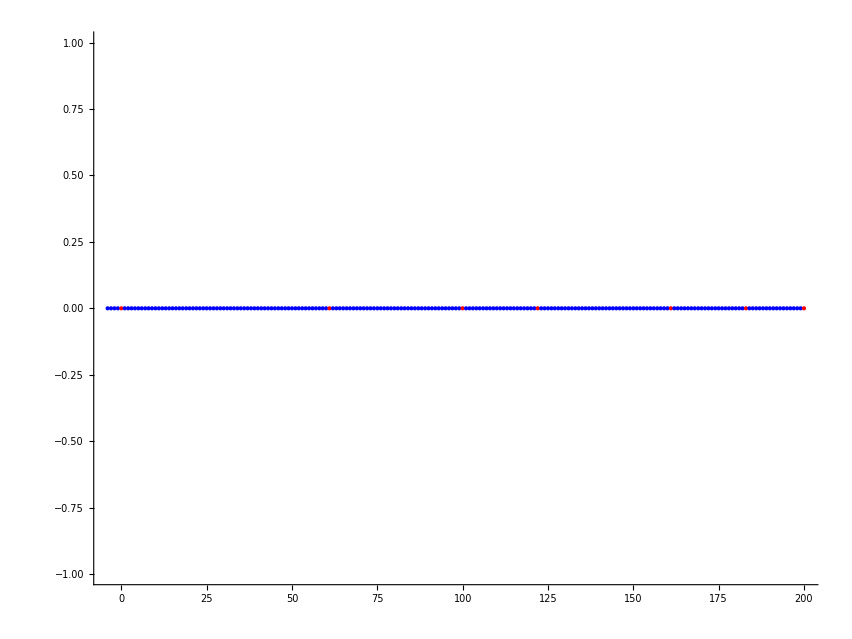

5939/2

Não falso?

```mathematica
(*Exercício 4.4*)
color[n_] := If[Length[FindInstance[{61 x + 100 y == n, x >= 0, y >= 0}, {x,y},Integers]]==0, Blue, Red]
Graphics[
Table[{color[n], Point[{n,0}]}, {n,-4,200}], Axes->{True,False}
]
(*todos os pontos menores que zero são azuis. todos os pontos acima de g(61,100) são vermelhos. para mais, zero é vermelho e g(61,100) é azul, pelo que o único ponto possível é o que reflete 0 em g(61,100) (caso contrário, ou era maior e refletia 0 num ponto vermelho, ou era menor e refletia g(61,100) num ponto azul). Falta então verificar que todos os pontos entre 0 e g(61,100) são refletidos para um ponto da cor oposta*)
p = (61 100 - 61 - 100)/2
Do[
If[Length[FindInstance[{61 x + 100 y == i, x >= 0, y >= 0}, {x,y},Integers]] ==
Length[FindInstance[{61 x + 100 y == 2p - i, x >= 0, y >= 0}, {x,y}, Integers]],Print["Falso!"];Break[]]
,{i,1,61 100 - 61 - 100}]
Print["Não falso?"]
(*Como o código acima imprime apenas "Não falso?", concluímos que o p obtido é o p desejado.*)
```

```mathematica
(*Exercício 5*)
(*Exercício 5.1*)
img=ImageResize[Import["https://i.imgur.com/CQh21E7.jpg"],{128,128}];
data = ImageData[img, Interleaving->False];
bw = 0.299data[[1]]+0.587data[[2]]+0.144data[[3]];
Image[bw]
(*este código retorna uma versão a preto e branco da imagem original*)
```

-Graphics-

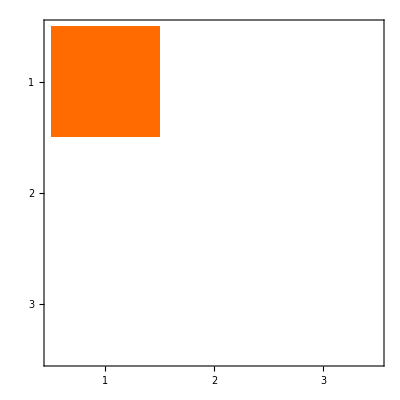
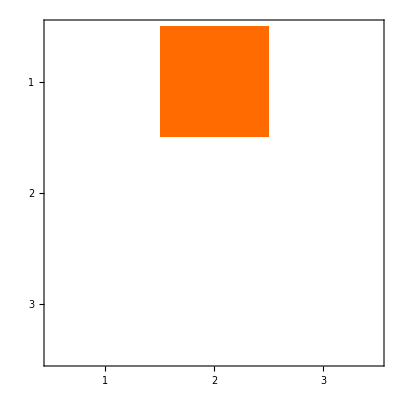
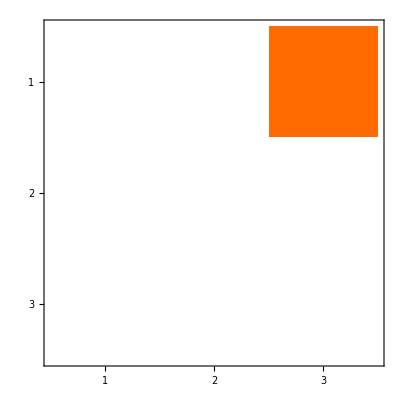
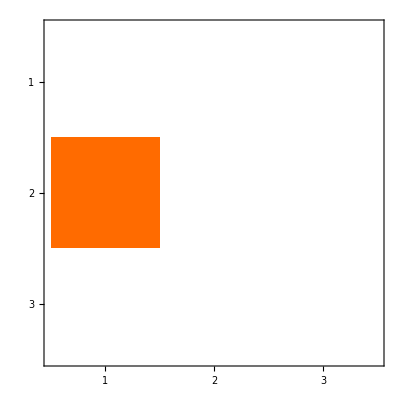
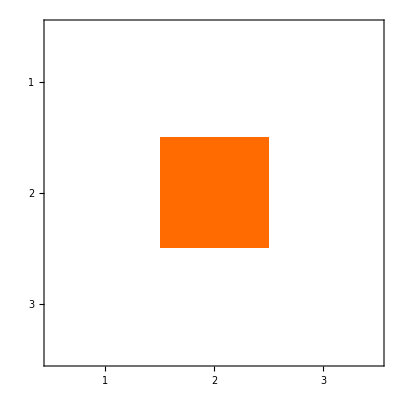
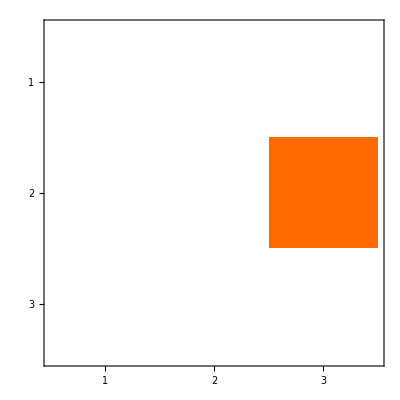
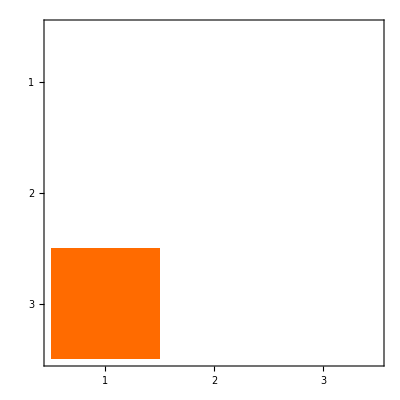
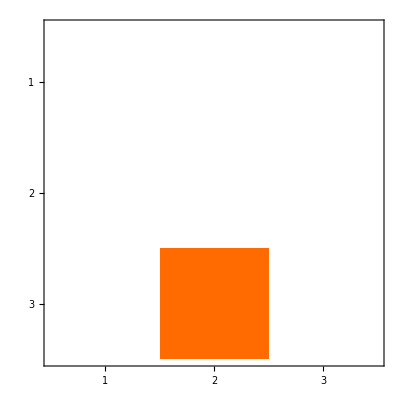

```mathematica
(*Exercício 5.2*)
canonical[n_,i_,j_] := Table[If[ii==i && jj==j, 1, 0], {ii,n},{jj,n}]
matrizes1[n_] := Flatten[Table[canonical[n,i,j],{i,n},{j,n}],1]
Map[MatrixPlot,matrizes1[3]]
```

```mathematica
(*Exercício 5.3*)
(*Usamos o comando Flatten para ver as matrizes como elementos de R^(n^2), e . para calcular o produto interno.*)
basis4 = Map[Flatten,matrizes1[4]];
Table[basis4[[i]].basis4[[j]], {i,4},{j,4}]//MatrixForm
(*Como a matriz dos produtos internos é a identidade, esta base é ortonormada.*)
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*Exercício 5.4*)
basisCoefficients[basis_,matrix_]:=Map[Flatten[#].Flatten[matrix]&,basis]
compressCoefficients[coefs_, epsilon_] := Table[If[Abs[coefs[[i]]]>epsilon,{coefs[[i]],i},Nothing],{i,Length[coefs]}]
decompress[compressedcoefs_,basis_] := Sum[c[[1]] basis[[c[[2]]]],{c,compressedcoefs}]
```

```mathematica
(*Exercício 5.5*)
basis1 = matrizes1[128];
```

```mathematica
coefs = basisCoefficients[basis1,bw];
```

```mathematica
compressed =compressCoefficients[coefs,0.5];
Image[decompress[compressed,basis1]]
Image[bw]
```

-Graphics-

-Graphics-

```mathematica
(*A distinção entre as imagens é que os pixeis escuros o suficiente ficaram pretos (foram "removidos"). Isto não é um algoritmo de compressão apropriado, porque não preserva a qualidade de imagem, simplesmente apaga tudo o que é escuro e não comprime nada que seja claro.*)
(*Este algoritmo manda fora todos os pixeis escuros, mas duplica a informação necessária para guardar todos os outros, visto que é necessário guardar a sua luminosidade e o índice da matriz correspondente. Assim sendo,este método guarda menos informação sse epsilon é superior à luminosidade mediana.*)
```

```mathematica
(*Exercício 5.6*)
AA[k_] := 1./k ArrayFlatten[
{{ConstantArray[1,{k,k/2}], ConstantArray[-1,{k,k/2}]}}
]
BB[k_] := 1./k ArrayFlatten[
{{ConstantArray[1,{k/2,k}]},
{ConstantArray[-1,{k/2,k}]}}
]
CC[k_] := 1./k ArrayFlatten[
{{ConstantArray[1,{k/2,k/2}], ConstantArray[-1,{k/2,k/2}]},
{ConstantArray[-1,{k/2,k/2}], ConstantArray[1,{k/2,k/2}]}}
]
```

```mathematica
(*testing*)
{AA[4],BB[4],CC[4]}//Map[MatrixForm]
```

{(0.25 | 0.25 | -0.25 | -0.25
0.25 | 0.25 | -0.25 | -0.25
0.25 | 0.25 | -0.25 | -0.25
0.25 | 0.25 | -0.25 | -0.25),(0.25 | 0.25 | 0.25 | 0.25
0.25 | 0.25 | 0.25 | 0.25
-0.25 | -0.25 | -0.25 | -0.25
-0.25 | -0.25 | -0.25 | -0.25),(0.25 | 0.25 | -0.25 | -0.25
0.25 | 0.25 | -0.25 | -0.25
-0.25 | -0.25 | 0.25 | 0.25
-0.25 | -0.25 | 0.25 | 0.25)}

```mathematica
paddings[m_, mult_,n_]:=(*assumes m is nxn matrix, makes mult^2 matrices of size (mult m) x (mult m) by padding with zeros as in problem statement*)
Flatten[
Table[ArrayPad[m,{{n (i-1),n (mult - i)},{n (j-1),n(mult-j)}}],{i,mult},{j,mult}]
,1]
```

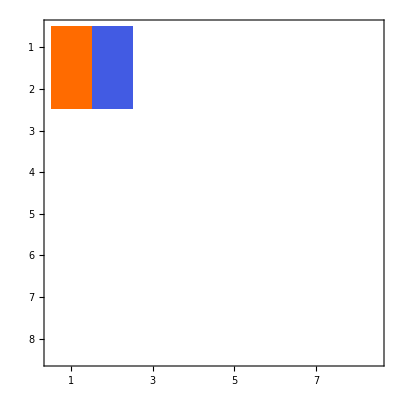
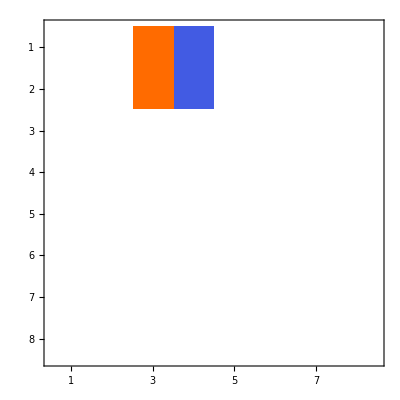
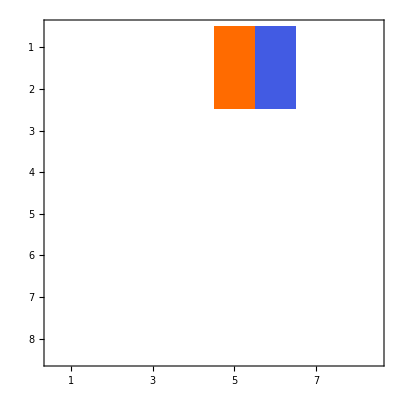
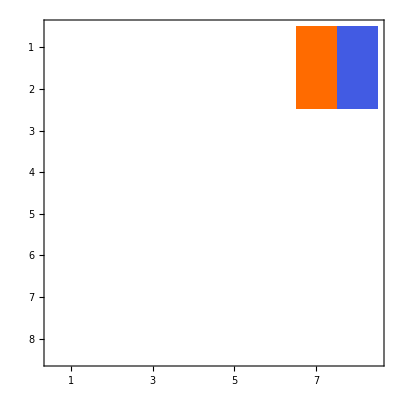
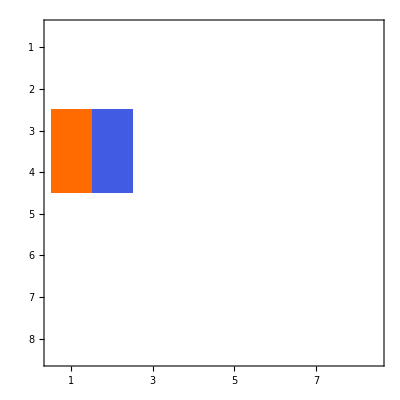
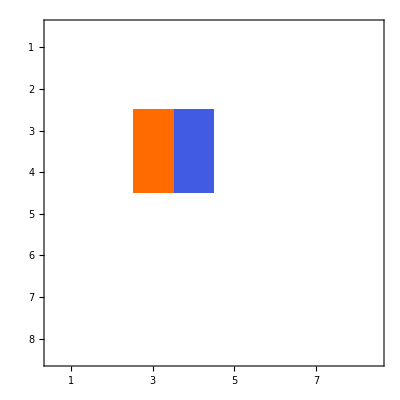
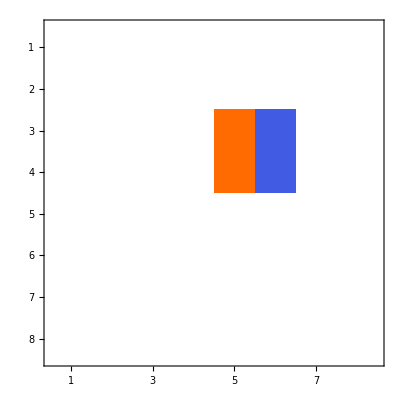
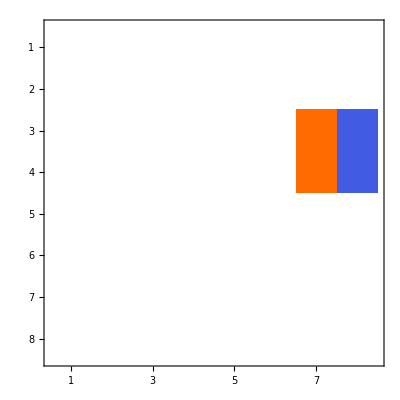

```mathematica
(*Checking that it works*)
paddings[AA[2],4,2]//Map[MatrixPlot]
```

```mathematica
typematrices[t_, n_]:=(*t is either AA, BB or CC and n is a power of two. makes the type-t matrices*)
Module[{list = {}, k = n},
While[k!= 1,
list = Join[list, paddings[t[k],n/k,k]];
k = k/2];
list]
```

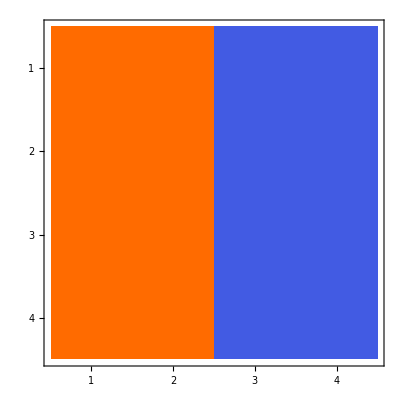
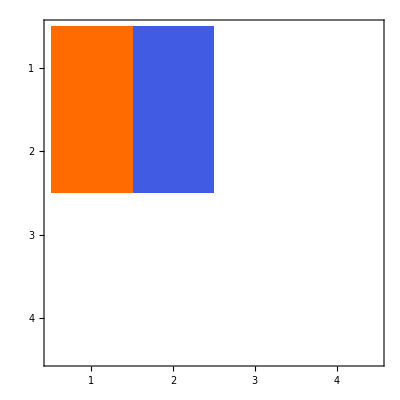
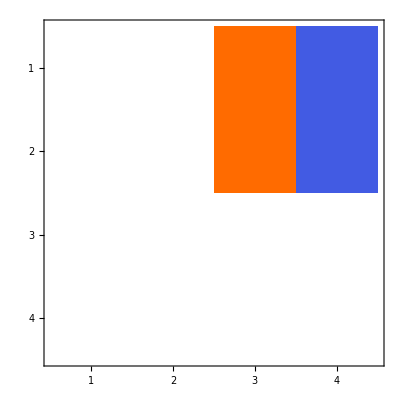
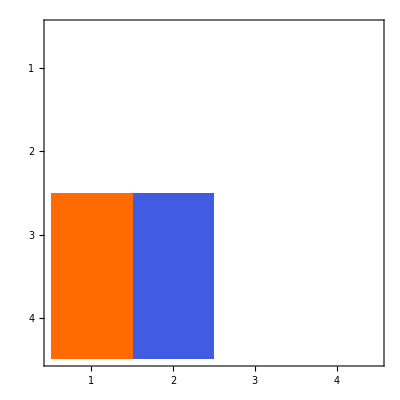
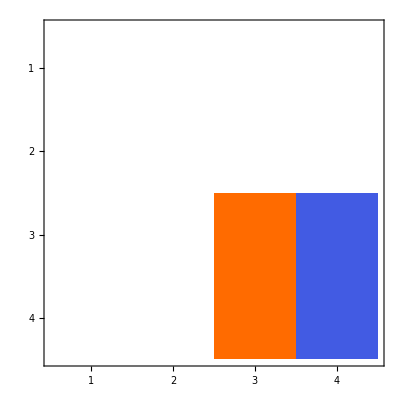

```mathematica
(*checking*)
typematrices[AA,4] // Map[MatrixPlot]
```

```mathematica
matrizes2[n_] :=
Join[{ConstantArray[1./n,{n,n}]}, typematrices[AA,n], typematrices[BB,n],typematrices[CC,n]]
```

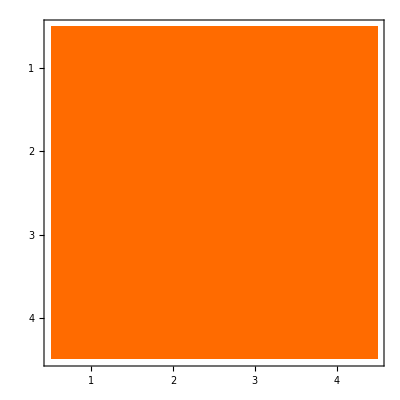
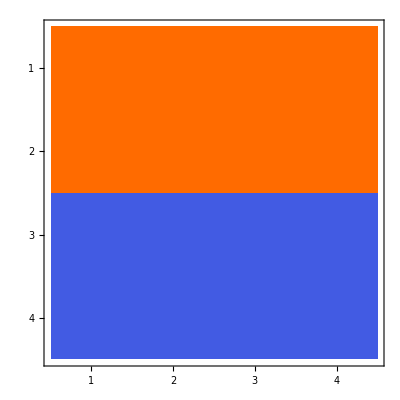
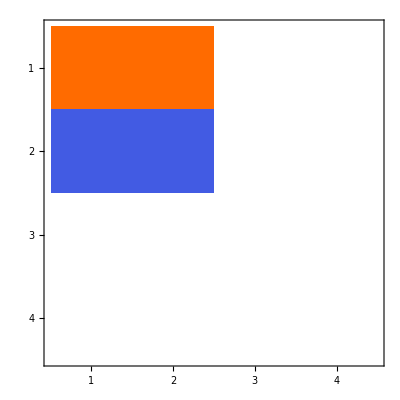
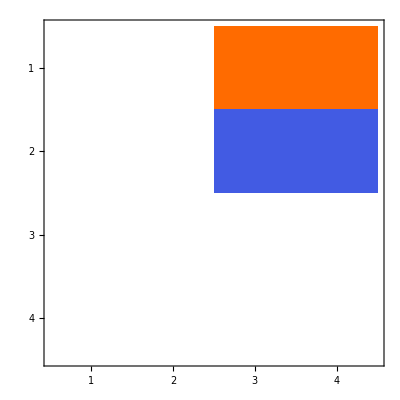
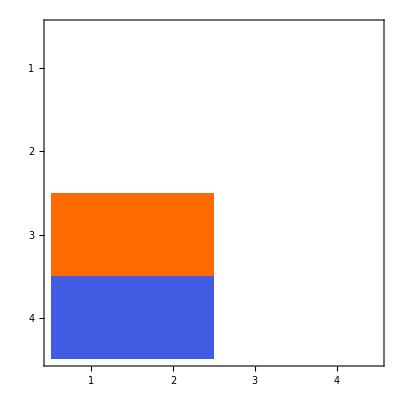
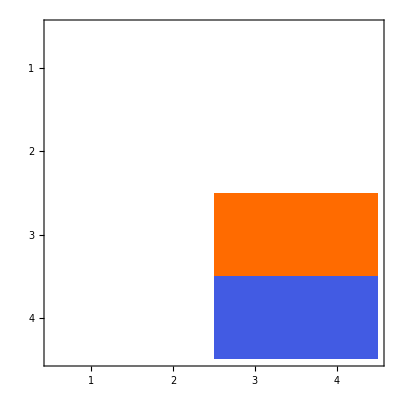
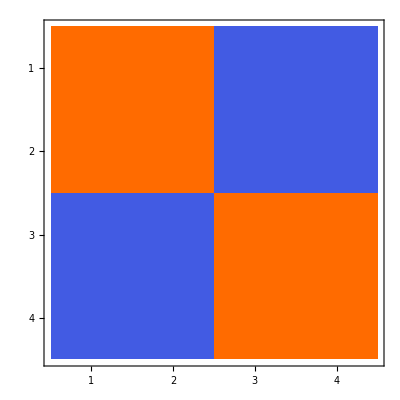
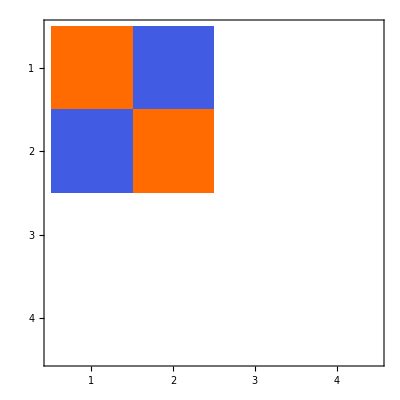
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
matrizes2[4]//Map[MatrixPlot]
```

```mathematica
basis2 = matrizes2[128];
coefs = basisCoefficients[basis2,bw];
```

```mathematica
compressed =compressCoefficients[coefs,0.5];
Image[decompress[compressed,basis2]]

compressed =compressCoefficients[coefs,0.2];
Image[decompress[compressed,basis2]]

compressed =compressCoefficients[coefs,0.1];
Image[decompress[compressed,basis2]]

Image[bw]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
(*Ao contrário da base canónica, a base ABC dá bons resultados.*)
```

```mathematica
(*Exercício 5.8*)
compressionratio[compressed_,original_] := Length[Flatten[compressed]]/Length[Flatten[original]]//N
```

```mathematica
compressed =compressCoefficients[coefs,0.5];
Image[decompress[compressed,basis2]]
compressionratio[compressed,bw]
(*Guardando apenas 1.8% da informação, obtemos uma imagem que não é muito boa e omite detalhes, mas consegue-se perceber o geral. neste caso, vê-se o vulto de um gatinho.*)
```

-Graphics-

0.0175781

```mathematica
compressed =compressCoefficients[coefs,0.1];
Image[decompress[compressed,basis2]]
compressionratio[compressed,bw]
(*Apesar de visivelmente "danificada", esta imagem é claramente idêntica à original, percebendo-se bem que é um gatinho sorrir*)
```

-Graphics-

0.195557

```mathematica
(*Sim, é possível o fator de compressão ser superior a 1. se guardarmos todos os coeficientes, guardamos um total de 2x128^2 números, visto que a versão comprimida tem de guardar dois números por cada coeficiente retido em vez de 1.*)
compressed =compressCoefficients[coefs,0.000001];
Image[decompress[compressed,basis2]]
compressionratio[compressed,bw]
```

-Graphics-

1.95227

```mathematica
(*Exercício 5.8*)
(*Vejamos primeiro a questão de espaço. Guardando as matrizes como as estamos a guardar, com muitos zeros e sem compressão nenhuma, cada matriz contém n^2 números, e há n^2 matrizes na base das matrizes nxn, pelo que a quantidade de números que é necessário guardar é n^4 para guardar a base das matrizes. para n=1024, isto é por volta de 10^12. sendo que cada GB guarda 2.7 x 10^8 números, a base ocupa por volta de 3700GB, o que é por volta de 3.5TB, que para além de ser muito mais do que os 32GB de memória de um computador normal, também é mais do que é possível guardar em maior parte dos discos de computadores.*)
(*Relativamente a tempo, vejamos o tempo do cálculo dos coeficientes. Há n^2 coeficientes para calcular. cada coeficiente requer n^2 contas de multiplicar e n-1 contas de somar, pelo que o número total de operações necessário para calcular os coeficientes é n^2 (n^2 + n - 1). Para n=1024, isto é aproximadamente 1.1 x 10^12. assumindo que um computador faz 10^8 operações por segundo (estimativa alta), é preciso aproximadamente 1.1 x 10^4 segundos para efetuar as contas todas, ou aproximadamente 3 horas. Isto é executável em tempo útil (assumindo que se ultrapassa o problema de espaço mencionado acima), mas é superior ao tempo que eu estaria disposto a esperar que o código corresse...*)
```